```mathematica
F[m_,eta_]:=NIntegrate[x^m/(Exp[x-eta]+1),{x,0,Infinity}]
```

```mathematica
F[3,0]/F[2,0.0]
```

3.15137

```mathematica
Sqrt[F[5,0.0]/F[3,0]]
```

4.56218

```mathematica
F[5,0]/F[3,0.0]
```

20.8135

```mathematica
F[5,1]
```

314.668

```mathematica
F[4,1]
```

60.9695

```mathematica
F[3,1]
```

14.3894

```mathematica
F[2,1]
```

4.32833

```mathematica
j=1
F[3+j,0]
```

1

23.3309

```mathematica
F[3,0]
```

5.6822

```mathematica
F[2,0]
```

1.80309

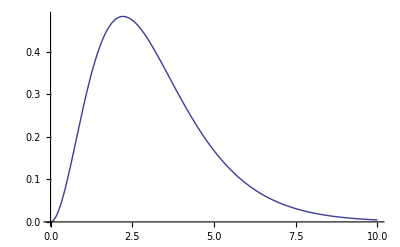

```mathematica
Plot[x^2/(Exp[x]+1),{x,0,10}]
```

```mathematica
(* free neutron and free proton scattering opacities *)
```

```mathematica
Clear[j,etanu]
sigma0=1.76*10^(-44)
sinsqTw=0.23
alpha=1.25
(* electron, mu, and tau types *)
Cv=1/2+2*sinsqTw
Csp=(4*(Cv-1)^2+5*alpha^2)/24
Csn=(1+5*alpha^2)/24
Yn=1-Yp
(*etan=etap=0*)
Ynn=Yn/(1+(2/3)*Max[etan,0])
Ypp=Yp/(1+(2/3)*Max[etap,0])
T=T11*10^(11)
rhob=rho10*10^(10)
Ksn=Csn*sigma0*rhob/mb*Ynn*(kb*T/(me*c^2))^2*FD[4+j,eta]/FD[2+j,eta]
Ksp=Csp*sigma0*rhob/mb*Ypp*(kb*T/(me*c^2))^2*FD[4+j,eta]/FD[2+j,eta]
```

1.76×10^-44

0.23

1.25

0.96

0.325788

0.367188

1-Yp

(1-Yp)/(1+2/3 Max[0,etan])

Yp/(1+2/3 Max[0,etap])

100000000000 T11

10000000000 rho10

(1.0981×10^-8 rho10 T11^2 (1-Yp) FD[4+j,eta])/(FD[2+j,eta] (1+2/3 Max[0,etan]))

(9.7429×10^-9 rho10 T11^2 Yp FD[4+j,eta])/(FD[2+j,eta] (1+2/3 Max[0,etap]))

```mathematica
Ksn//.{rhob->rho10*10^(10),T->T11*10^(11)}
```

(1.0981×10^-8 rho10 T11^2 (1-Yp) FD[4+j,eta])/(FD[2+j,eta] (1+2/3 Max[0,etan]))

```mathematica
Ksp//.{rhob->rho10*10^(10),T->T11*10^(11)}
```

(9.7429×10^-9 rho10 T11^2 Yp FD[4+j,eta])/(FD[2+j,eta] (1+2/3 Max[0,etap]))

```mathematica
Ksn*F[5,0]/F[3,0.0]
Ksp*F[5,0]/F[3,0.0]
```

(2.28552×10^-7 rho10 T11^2 (1-Yp) FD[4+j,eta])/(FD[2+j,eta] (1+2/3 Max[0,etan]))

(2.02783×10^-7 rho10 T11^2 Yp FD[4+j,eta])/(FD[2+j,eta] (1+2/3 Max[0,etap]))

```mathematica
Ks=Collect[Expand[FullSimplify[Ksn+Ksp]],{T,rhob,Yp}]
```

rhob T^2 ((1.64354×10^-40 FF[5,eta])/(FF[3,eta] (3.+2. Max[0.,etan]))+Yp ((1.27413×10^-40 FF[5,eta])/(FF[3,eta] (3+2 Max[0,etap]))-(1.64354×10^-40 FF[5,eta])/(FF[3,eta] (3.+2. Max[0.,etan]))))

```mathematica
Ksfinal=FullSimplify[Ks//.{rhob->rho10*10^(10.0),T->T11*10^(11.0)}]
```

(rho10 T11^2 FF[5,eta] (4.93063×10^-8-1.10826×10^-8 Yp+2.54825×10^-8 Yp Max[0.,etan]+(3.28709×10^-8-3.28709×10^-8 Yp) Max[0.,etap]))/(FF[3,eta] (3.+2. Max[0.,etan]) (3.+2. Max[0.,etap]))

```mathematica
FullSimplify[Ksfinal/(3.04385*10^(-7))]
```

3.28531×10^6 rho10 T11^2 ((3.04385×10^-7 Yp)/(1.5+1. Max[0,etap])+(3.42593×10^-7-3.42593×10^-7 Yp)/(1.5+1. Max[0.,etan]))

```mathematica
FullSimplify[3.2853130081968564*^6 *3.0438466803515565*^-7 *rho10 T11^2 ((3.0438466803515565*^-7 Yp)/((1.5+1. Max[0,etap])*(3.0438466803515565*^-7 ))+(3.42592629256476*^-7-3.42592629256476*^-7 Yp)/((1.5+1. Max[0.,etan])*3.0438466803515565*^-7))]
```

0.999999 rho10 T11^2 ((1. Yp)/(1.5+1. Max[0,etap])+(1.12553-1.12553 Yp)/(1.5+1. Max[0.,etan]))

```mathematica
(* so above agrees with what I'm using within a factor of <2 for coefficient *)
```

```mathematica
(* now do electron scattering *)
```

```mathematica
3.2853130081968564*^6 *3.0438466803515565*^-7
```

0.999999

5.97452×10^23 rhob Yp

```mathematica
(* ELECTRON SCATTERING *)
```

```mathematica
ne=rhob/mb*Yp
j=1
etanu=0
Clear[j,etanu]
sinsqTw=0.23
```

5.97452×10^33 rho10 Yp

1

0

0.23

```mathematica
(* j=0 for number and j=1 for energy *)
```

```mathematica
(* nu_e *)
CA=1/2
Cv=1/2+2*sinsqTw
Ksnue1=ne*3*sigma0/8*(kb*T/(me*c^2))^2*(1+etae/4)*((Cv+CA)^2+1/3*(Cv-CA)^2)*FD[3+j,etanue]/FD[2+j,etanue]
(* \bar{\nu_e} *)
CA=-1/2
Cv=1/2+2*sinsqTw
Ksnue2=ne*3*sigma0/8*(kb*T/(me*c^2))^2*(1+etae/4)*((Cv+CA)^2+1/3*(Cv-CA)^2)*FD[3+j,etanuebar]/FD[2+j,etanuebar]
(* nu_mu *)
CA=-1/2
Cv=-1/2+2*sinsqTw
Ksnue3=ne*3*sigma0/8*(kb*T/(me*c^2))^2*(1+etae/4)*((Cv+CA)^2+1/3*(Cv-CA)^2)*FD[3+j,etanu]/FD[2+j,etanu]
(* \bar{\nu_mu} *)
CA=1/2
Cv=-1/2+2*sinsqTw
Ksnue4=ne*3*sigma0/8*(kb*T/(me*c^2))^2*(1+etae/4)*((Cv+CA)^2+1/3*(Cv-CA)^2)*FD[3+j,etanu]/FD[2+j,etanu]
(* nu_tau *)
CA=-1/2
Cv=-1/2+2*sinsqTw
Ksnue5=ne*3*sigma0/8*(kb*T/(me*c^2))^2*(1+etae/4)*((Cv+CA)^2+1/3*(Cv-CA)^2)*FD[3+j,etanu]/FD[2+j,etanu]
(* \bar{\nu_mu} *)
CA=1/2
Cv=-1/2+2*sinsqTw
Ksnue6=ne*3*sigma0/8*(kb*T/(me*c^2))^2*(1+etae/4)*((Cv+CA)^2+1/3*(Cv-CA)^2)*FD[3+j,etanu]/FD[2+j,etanu]
```

1/2

0.96

(2.46961×10^-8 (1+etae/4) rho10 T11^2 Yp FD[3+j,etanue])/FD[2+j,etanue]

-1/2

0.96

(1.03414×10^-8 (1+etae/4) rho10 T11^2 Yp FD[3+j,etanuebar])/FD[2+j,etanuebar]

-1/2

-0.04

(4.06119×10^-9 (1+etae/4) rho10 T11^2 Yp FD[3+j,etanu])/FD[2+j,etanu]

1/2

-0.04

(3.46308×10^-9 (1+etae/4) rho10 T11^2 Yp FD[3+j,etanu])/FD[2+j,etanu]

-1/2

-0.04

(4.06119×10^-9 (1+etae/4) rho10 T11^2 Yp FD[3+j,etanu])/FD[2+j,etanu]

1/2

-0.04

(3.46308×10^-9 (1+etae/4) rho10 T11^2 Yp FD[3+j,etanu])/FD[2+j,etanu]

```mathematica
Ksel=Ksnue1+Ksnue2
Ksmu=Ksnue3+Ksnue4
Kstau=Ksnue5+Ksnue6
```

(2.46961×10^-8 (1+etae/4) rho10 T11^2 Yp FD[3+j,etanue])/FD[2+j,etanue]+(1.03414×10^-8 (1+etae/4) rho10 T11^2 Yp FD[3+j,etanuebar])/FD[2+j,etanuebar]

(7.52427×10^-9 (1+etae/4) rho10 T11^2 Yp FD[3+j,etanu])/FD[2+j,etanu]

(7.52427×10^-9 (1+etae/4) rho10 T11^2 Yp FD[3+j,etanu])/FD[2+j,etanu]

```mathematica
Ksnue=FullSimplify[Ksnue1//.{rhob->rho10*10^(10.0),T->T11*10^(11.0)}]
Ksnuebar=FullSimplify[Ksnue2//.{rhob->rho10*10^(10.0),T->T11*10^(11.0)}]
```

(6.17403×10^-9 (4.+etae) rho10 T11^2 Yp FD[3+j,etanue])/FD[2+j,etanue]

(2.58535×10^-9 (4.+etae) rho10 T11^2 Yp FD[3+j,etanuebar])/FD[2+j,etanuebar]

```mathematica
Eth=F[4,0.0]/F[3,0.0]
```

4.10596

```mathematica
Ksnue*Eth
Ksnuebar*Eth
```

(2.53503×10^-8 (4.+etae) rho10 T11^2 Yp FD[3+j,etanue])/FD[2+j,etanue]

(1.06153×10^-8 (4.+etae) rho10 T11^2 Yp FD[3+j,etanuebar])/FD[2+j,etanuebar]

```mathematica
Ksel=FullSimplify[Ksel//.{rhob->rho10*10^(10.0),T->T11*10^(11.0)}]
Ksmu=FullSimplify[Ksmu//.{rhob->rho10*10^(10.0),T->T11*10^(11.0)}]
Kstau=FullSimplify[Kstau//.{rhob->rho10*10^(10.0),T->T11*10^(11.0)}]
```

1/4 (4+etae) rho10 T11^2 Yp ((2.46961×10^-8 FD[3+j,etanue])/FD[2+j,etanue]+(1.03414×10^-8 FD[3+j,etanuebar])/FD[2+j,etanuebar])

(1.88107×10^-9 (4.+etae) rho10 T11^2 Yp FD[3+j,etanu])/FD[2+j,etanu]

(1.88107×10^-9 (4.+etae) rho10 T11^2 Yp FD[3+j,etanu])/FD[2+j,etanu]

```mathematica
Ksmu*Eth
Kstau*Eth
```

(7.72359×10^-9 (4.+etae) rho10 T11^2 Yp FD[3+j,etanu])/FD[2+j,etanu]

(7.72359×10^-9 (4.+etae) rho10 T11^2 Yp FD[3+j,etanu])/FD[2+j,etanu]

1.28503×10^-7 (4.+etae) rho10 T11^2 Yp

```mathematica
(* heavy nuclei *)
```

```mathematica
j=1
etanu=0
Clear[j,etanu]
rhobbound=rhob*(1-xnuc)
na=rhobbound/(amu*abar)
Clear[na]
mA=(mb*abar)
na = rhobA/mA
KsnuA=na*sigma0/16*(kb*T/(me*c^2))^2*FD[4+j,etanu]/FD[2+j,etanu]
KsnuA=FullSimplify[KsnuA//.{rhobA->rhobA10*10^(10.0),T->T11*10^(11.0)}]
```

1

0

rhob (1-xnuc)

(6.02214×10^23 rhob (1-xnuc))/abar

1.67377×10^-24 abar

(5.97452×10^23 rhobA)/abar

(1.86911×10^-41 rhobA T^2 FD[4+j,etanu])/(abar FD[2+j,etanu])

(1.86911×10^-9 rhobA10 T11^2 FD[4+j,etanu])/(abar FD[2+j,etanu])

```mathematica
(F[5,0]/F[3,0.0])
```

20.8135

```mathematica
1.8691054001176083*^-9*(F[5,0]/F[3,0.0])
```

3.89025×10^-8

```mathematica
(* shapiro prefactor *)
```

```mathematica
shapiroA=1/16*A^2*(1-Z/A+(4*sinsqTw-1)*Z/A)^2
```

1/16 A^2 (1-(1.08 Z)/A)^2

```mathematica
shapiroA//.{Z->A/2,A->56}
```

41.4736

```mathematica
W=1-2*Z/A*(1-2*sinsqTw)
Clos=Z/A*(1+4*sinsqTw)/(2)
burrowsA=4*Pi/(64*Pi)*A^2*(W+Clos)^2
```

1-(1.08 Z)/A

(0.96 Z)/A

1/16 A^2 (1-(0.12 Z)/A)^2

```mathematica
Esq = FD[4+j,etanu]/FD[2+j,etanu]*(kb*T)^2
E1=33*ergPmev*(rho/10^(12))^(1/3) (* Shapiro calculation *)
Esq=E1^2
Clear[Esq]
Esq=EsqperkbTsq*(kb*T)^2
sigmaAcoh=1/16*sigma0*Esq*(1/(me*c^2))^2*A^2*(1-Z/A+(4*sinsqTw-1)*Z/A)^2
KbAcoh=sigmaAcoh/(A*amu)
tauAcoh=KbAcoh*rho*H//.{rho->rho10*10^(10),T->T11*10^11}
```

(1.90633×10^-32 T^2 FD[4+j,etanu])/FD[2+j,etanu]

5.28718×10^-9 rho^(1/3)

2.79543×10^-17 rho^(2/3)

1.90633×10^-32 EsqperkbTsq T^2

3.12846×10^-65 A^2 EsqperkbTsq T^2 (1-(1.08 Z)/A)^2

1.884×10^-41 A EsqperkbTsq T^2 (1-(1.08 Z)/A)^2

1.884×10^-9 A EsqperkbTsq H rho10 T11^2 (1-(1.08 Z)/A)^2

```mathematica
god=tauAcoh//.{A->56,Z->A/2,rho10->rho12*10^(2)}
```

0.0000327367 H rho12^(5/3)

```mathematica
god//.{rho12->rho/10^(12)}//.{rho->3.698*10^9}//.{H->3.8*10^8}
```

1.10009

```mathematica
god=F[5,0.0]/F[3,0.0]
1.884001807755023*^-9 *god*56
```

20.8135

2.1959×10^-6

```mathematica
KsnuA*56
```

-(2.1959×10^-6 rho10 T11^2 (-1.+xnuc))/abar

```mathematica
(* larger than Shapiro for Ye=0.5 by factor of 3 *)
```

```mathematica
yetotlocal=0.0
1.4578*(1.0-1.08*yetotlocal)/(2.1959)
```

0.

0.663874

```mathematica
6*8
```

48

```mathematica
36/9.0
```

4.

```mathematica
3.4/0.7
```

4.85714

```mathematica
sinTw=0.23
ca=1/2
cv=1/2+2*sinTw
C1C2ele=(cv-ca)^2+(cv+ca)^2
C1C2mutau=(cv-ca)^2+(cv+ca-2)^2
```

0.23

1/2

0.96

2.3432

0.5032

```mathematica
qpairele=0.5*C1C2ele/36*sigma0*c/(me*c^2)^2*(kb*T)^9
qpairmutau=0.5*C1C2mutau/9*sigma0*c/(me*c^2)^2*(kb*T)^9
```

4.67136×10^-166 T^9

4.01268×10^-166 T^9

```mathematica
qpairele//.{T->T11*10^(11)}
qpairmutau//.{T->T11*10^(11)}
```

4.67136×10^-67 T11^9

8.02536×10^-67 T11^9

```mathematica
1/Sqrt[3.0]
```

0.57735

```mathematica
qdotpairelekaz=3.4*10^(33)*T11^9
qdotpairelekaz=0.7*10^(33)*T11^9
qdotpairelekaz/(kb*T)//.{T->T11*10^(11)}
```

3.4×10^33 T11^9

7.×10^32 T11^9

5.06989×10^37 T11^8

```mathematica
1/Sqrt[3.0]
```

0.57735

```mathematica
(* brem as in KM02 *)
```

```mathematica
qdotnondegen=1.5*10^(33)*T11^5.5*(rho/10^(13))^2//.{rho->rho10*10^(10)}
```

1.5×10^27 rho10^2 T11^5.5

```mathematica
qdotdegen=3.4*10^(33)*T11^8*(rho/(10^(13)))^(1/3)//.{rho->rho10*10^(10)}
```

3.4×10^32 rho10^(1/3) T11^8

```mathematica
(* Fake number rates *)
```

```mathematica
qdotnondegen/(3.15*kb*T)//.{T->T11*10^(11)}
qdotdegen/(3.15*kb*T)//.{T->T11*10^(11)}
```

3.44891×10^31 rho10^2 T11^4.5

7.81752×10^36 rho10^(1/3) T11^7

```mathematica
30*1024*1024/350./60/60
```

24.9661

```mathematica
Ye=1/(1+x)
FullSimplify[(2*Ye-1)/(1-Ye)]
```

1/(1+x)

-1+1/x

```mathematica
2.1959*10^(-6)*(1-1.08*yeA)^2//.{yeA->1/2}
```

4.64652×10^-7

```mathematica
Solve[2.1785*10^(-6)==2.1959*10^(-6)*(1-1.08*yeA)^2,yeA]
```

{{yeA→0.00367575},{yeA→1.84818}}

```mathematica
Plot[
```

```mathematica
fun=1-ye+(4*0.23-1)*ye
```

1-1.08 ye

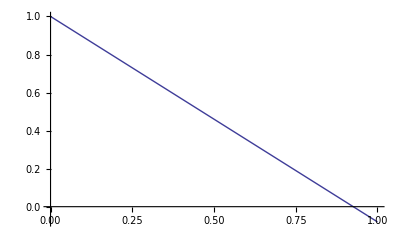

```mathematica
Plot[fun,{ye,0,1}]
```

```mathematica
fun//.{ye->0.93}
```

-0.0044

```mathematica
Solve[fun==0,ye]
```

{{ye→0.925926}}